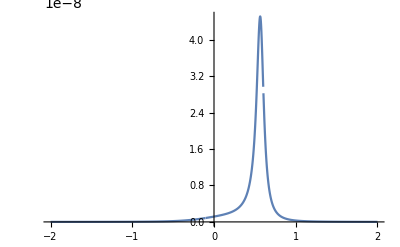

$Aborted

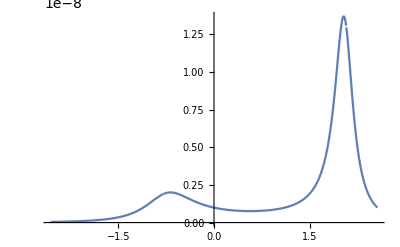

```mathematica
MHz=10^6;
Γ1=5.3*2*π MHz;
Γ2=15.1*2*π MHz;
Γ=Γ1+Γ2;
a=1/2;
Ω=a (Γ1+Γ2);
Δ1=Γ/2;
Ωtilde=√(Abs[Ω]^2+Δ1^2);
ΔS=-Δ1/2+Sign[Δ1]/(2 √2)√(Ωtilde^2-Γ^2/4+√((Ωtilde^2-Γ^2/4)^2+Δ1^2 Γ^2));
κ=Γ ΔS/(Δ1+2ΔS);
S0[Δ2_]=(Abs[Ω]^2/4 Γ/(2 π))/Abs[(Δ2-Δ1-ΔS+ⅈ κ/2)(Δ2+ΔS+ⅈ (Γ-κ)/2)]^2;
Plot[S0[x Γ],{x,-2,2},PlotRange->All]
Plot[FourierTransform[S0[x Γ],x,t],{t,-1/2,1/2},PlotRange->All]
```

```mathematica
Ωtildex=√(Abs[Ωx]^2+Δ1x^2);
ΔSx=-Δ1x/2+Sign[Δ1x]/(2 √2)√(Ωtildex^2-Γx^2/4 √((Ωtildex^2-Γx^2/4)^2+Δ1x^2 Γx^2));
κx=Γx ΔSx/(Δ1x+2ΔSx);
```

0

```mathematica
Limit[κx,Δ1x->0]
Limit[ΔSx,Δ1x->0]
```

Γx/2

1/8 √(8 Abs[Ωx]^2-1/2 Γx^2 √((Γx^2-4 Abs[Ωx]^2)^2))

```mathematica
Limit[(Abs[Ωx]^2/4 Γx/(2 π))/Abs[(Δ2-Δ1x-ΔSx+ⅈ κx/2)(Δ2+ΔSx+ⅈ (Γx-κx)/2)]^2,Δ1x->0]
```

(Γx Abs[Ωx]^2)/(8 π Abs[(ⅈ Γx Δ2)/2+Δ2^2-Abs[Ωx]^2/8+1/128 Γx^2 (-8+√((Γx^2-4 Abs[Ωx]^2)^2))]^2)

```mathematica
(Γx Abs[Ωx]^2)/(8 π Abs[(ⅈ Γx Δ2)/2+Δ2^2-Abs[Ωx]^2/8+1/128 Γx^2 (-8+√((Γx^2-4 Abs[Ωx]^2)^2))]^2)/.Ωx->0
```

0